```mathematica
NS["study_fact_moments_weights","C:\\Users\\pglpm\\repositories\\maxNt\\scripts"]
```

```mathematica
fm[n_,r_]:=(Binomial[#,r]/Binomial[n,r])&/@Range[0,n]
```

```mathematica
N[{fm[10,3],1-fm[10,3]}]//MF
```

(0. | 0. | 0. | 0.00833333 | 0.0333333 | 0.0833333 | 0.166667 | 0.291667 | 0.466667 | 0.7 | 1.
1. | 1. | 1. | 0.991667 | 0.966667 | 0.916667 | 0.833333 | 0.708333 | 0.533333 | 0.3 | 0.)

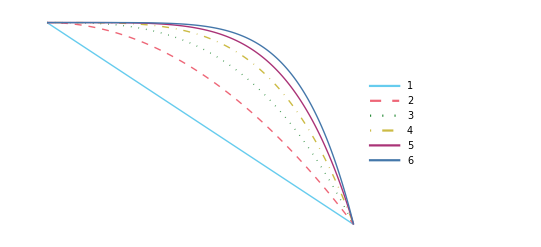

```mathematica
ListPlot[1-Table[fm[1000,r],{r,6}],Joined->True,PlotRange->All,PlotLegends->Auto]
```

```mathematica
Total[fm[10,3]]
```

11/4